```mathematica
Solve[a{1,2}+b{2,1}=={6,6}]
```

{{a→2,b→2}}

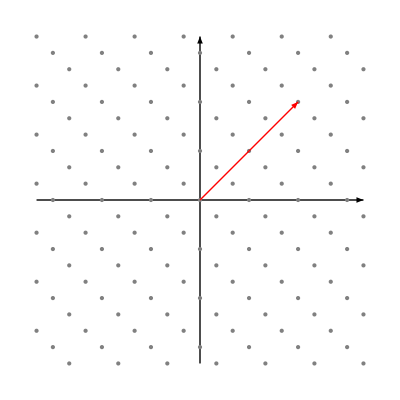

```mathematica
Graphics[{
{Thick,Arrow[{{-10,0},{10,0}}]},
{Thick,Arrow[{{0,-10},{0,10}}]},
{Gray,Table[Table[Point[i{1,2}+j{2,1}],{i,-10,10}],{j,-10,10}]},
{Red,Thick,Arrow[{{0,0},{6,6}}]},
},PlotRange->{{-10,10},{-10,10}}]
```

```mathematica
?Arrow
```

Arrow[{pt_1,pt_2}] is a graphics primitive that represents an arrow from pt_1 to pt_2.
Arrow[{pt_1,pt_2},s] represents an arrow with its ends set back from pt_1 and pt_2 by a distance s. 
Arrow[{pt_1,pt_2},{s_1,s_2}] sets back by s_1 from pt_1 and s_2 from pt_2. 
Arrow[curve,…] represents an arrow following the specified curve.

```mathematica
?Mod
```

Mod[m,n] gives the remainder on division of m by n. 
Mod[m,n,d] uses an offset d.

```mathematica
Mod[Table[i,{i,1,10}],2,1]
```

{1,2,1,2,1,2,1,2,1,2}